### 2.a make a plot, in the parameter space (α,k), of the first (the one near α=0.5) instability tongue of the lower fixed point z_=(0,0)

```mathematica
(*Similar to the former case, we try to solve its linearization. With some calculation: *)
XL[{α_,k_}][{x_,v_,t_}]:={v,-α^2/(1+k Cos[t])x+(2k Sin[t])/(1+k Cos[t])v,1}
AlgoL[αk_,h_][xvt_]:=xvt+h XL[αk][xvt+h/2 XL[αk][xvt]]
AlgoL[{αk[[1]],αk[[2]]},h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
```

Part::partd: Part specification αk⟦1⟧ is longer than depth of object.

Part::partd: Part specification αk⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),xvt⟦2⟧+h (-((xvt⟦1⟧+1/2 h xvt⟦2⟧) αk⟦1⟧^2)/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),h+xvt⟦3⟧}

```mathematica
AlgoL=Compile[{{αk,_Real,1},h,{xvt,_Real,1}},{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),xvt⟦2⟧+h (-((xvt⟦1⟧+1/2 h xvt⟦2⟧) αk⟦1⟧^2)/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(xvt⟦1⟧ αk⟦1⟧^2)/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),h+xvt⟦3⟧}];
```

```mathematica
SolL=Compile[{{αk,_Real,1},ndiv,{xv,_Real,1}},Take[Nest[AlgoL[αk,(2π)/ndiv,#]&,Append[xv,0],ndiv],2]];
```

```mathematica
PML[αk_,ndiv_]:={SolL[αk,ndiv,{1,0}],SolL[αk,ndiv,{0,1}]}
```

```mathematica
akTr[αk_,ndiv_]:={αk,Abs[Tr[PML[αk,ndiv]]]}
```

```mathematica
RTr[rgx_,rgy_,ndiv_]:=akTr[{RandomReal[rgx],RandomReal[rgy]},ndiv]
```

```mathematica
crTr[prec_][el_]:=el[[2]]>2+prec
```

```mathematica
PlInstTr[lst_,prec_,rgx_,rgy_]:=ListPlot[Transpose[Select[lst,crTr[prec]]][[1]],PlotRange->{rgx,rgy}]
```

```mathematica
rg0x={0,1};rg0y={0,1.2};
pts0=Table[RTr[rg0x,rg0y,100],20000];
```

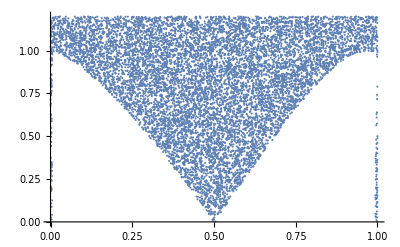

```mathematica
PlInstTr[pts0,-.001,rg0x,rg0y]
```

```mathematica
(*At α=0 or 1, the dynamical system is not well-defined, and the graph appears strange. *)
```

```mathematica
(*And a clearer look near α=0.5: *)
rg1x={.45,.55};rg1y={0,.2};
pts1=Table[RTr[rg1x,rg1y,100],20000];
```

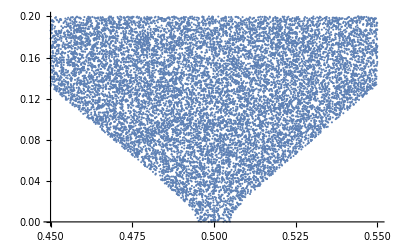

```mathematica
PlInstTr[pts1,-.001,rg1x,rg1y]
```

### 2.b make some plots showing the change in the structure of the phase portrait near z_=(0,0) at the entrance into (and/or exit from) the first instability tongue.

```mathematica
(*Instead of the linearization, we now need to look into the original problem: *)
X[{α_,k_}][{x_,v_,t_}]:={v,-α^2/(1+k Cos[t])Sin[x]+(2k Sin[t])/(1+k Cos[t])v,1}
```

```mathematica
Algo[αk_,h_][xvt_]:=xvt+h X[αk][xvt+h/2 X[αk][xvt]]
Algo[{αk[[1]],αk[[2]]},h][{xvt[[1]],xvt[[2]],xvt[[3]]}]
```

Part::partd: Part specification αk⟦1⟧ is longer than depth of object.

Part::partd: Part specification αk⟦2⟧ is longer than depth of object.

Part::partd: Part specification xvt⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),xvt⟦2⟧+h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧+1/2 h xvt⟦2⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),h+xvt⟦3⟧}

```mathematica
Algo=Compile[{{αk,_Real,1},h,{xvt,_Real,1}},{xvt⟦1⟧+h (xvt⟦2⟧+1/2 h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))),xvt⟦2⟧+h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧+1/2 h xvt⟦2⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)+(2 αk⟦2⟧ (xvt⟦2⟧+1/2 h (-(αk⟦1⟧^2 Sin[xvt⟦1⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧)+(2 xvt⟦2⟧ αk⟦2⟧ Sin[xvt⟦3⟧])/(1+Cos[xvt⟦3⟧] αk⟦2⟧))) Sin[h/2+xvt⟦3⟧])/(1+Cos[h/2+xvt⟦3⟧] αk⟦2⟧)),h+xvt⟦3⟧}];
```

```mathematica
Sol=Compile[{{αk,_Real,1},ndiv,{xv,_Real,1}},Take[Nest[Algo[αk,(2π)/ndiv,#]&,Append[xv,0],ndiv],2]];
```

```mathematica
(*And we obtain the period shifting map: *)
PSM=Compile[{{αk,_Real,1},{ndiv,_Integer},{xv,_Real,1}},
Take[     Nest[Algo[αk,(2π)/ndiv,#]&,Append[xv,0],ndiv]   , 2]];
```

```mathematica
(*The orbit of PSM: *)
OrbPSM[αk_,ndiv_,nit_,xv_]:=NestList[ PSM[αk,ndiv,#]&,xv,nit]
(*where nit is the time of iteration (of PSM). *)
```

```mathematica
(*Plot the orbit: *)
GOrbPSM[αk_,ndiv_,nit_,xv_,plrg_]:=ListPlot[OrbPSM[αk,ndiv,nit,xv],PlotRange->plrg]
```

```mathematica
(*For convenience I copy the picture of the parametric space near α=0.5: *)
PlInstTr[pts1,-.001,rg1x,rg1y]
```

-Graphics-

```mathematica
(*Take a point (α,k) outside and near the instability tongue, for example, (α,k)=(0.48,0.04): *)
αk0={0.48,0.04};
```

```mathematica
orb0[xv_]:=GOrbPSM[αk0,100,1000,xv,{{-2,2},{-1,1}}]
```

```mathematica
orb00=orb0[0.01{.5,.5}];
```

```mathematica
orb01=orb0[0.1{.5,.5}];
```

```mathematica
orb02=orb0[0.3{.5,.5}];
```

```mathematica
orb03=orb0[0.6{.5,.5}];
```

```mathematica
orb04=orb0[{.5,.5}];
```

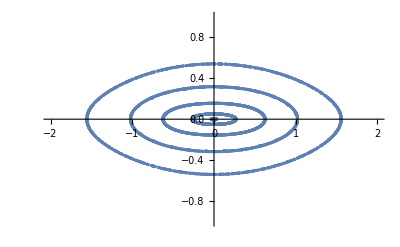
-Graphics-(α,k)=(0.48,0.04), outside & entering instability tongue

```mathematica
Labeled[Show[orb00, orb01,orb02,orb03,orb04],Style["(α,k)=(0.48,0.04), outside & entering instability tongue","Graphics"]]
```

```mathematica
(*Take a point (α,k) inside and near the instability tongue: (α,k)=(0.5,0.01): *)
```

```mathematica
αk1={0.5,0.01};
```

```mathematica
orb1[xv_]:=GOrbPSM[αk1,100,1000,xv,{{-2,2},{-1,1}}];
```

```mathematica
orb10=orb1[0.01{.5,.5}];
```

```mathematica
orb11=orb1[0.3{.5,.5}];
```

```mathematica
orb12=orb1[0.6{.5,.5}];
```

```mathematica
orb13=orb1[{.5,.5}];
```

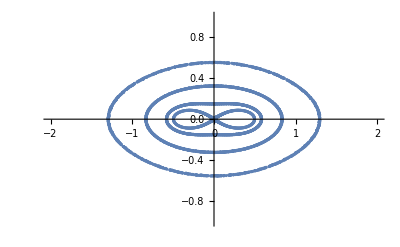
-Graphics-(α,k)=(0.5,0.01), inside instability tongue

```mathematica
Labeled[Show[orb10,orb11,orb12,orb13],Style["(α,k)=(0.5,0.01), inside instability tongue","Graphics"]]
```

```mathematica
(*Take a point (α,k) exiting the instability tongue: (α,k)=(0.52,0.03); here I want a clearer look so I am using different colors: *)
αk2={0.52,0.03};
```

```mathematica
orb2[nit_,xv_,color_]:=ListPlot[OrbPSM[αk2,100,nit,xv],PlotRange->{{-2,2},{-1,1}},PlotStyle->color]
```

```mathematica
orb20=orb2[1000,0.01{.5,.5},Red];
```

```mathematica
orb21=orb2[2000,0.2{.5,.5},Orange];
```

```mathematica
orb22=orb2[2000,0.3{.5,.5},Green];
```

```mathematica
orb24=orb2[1000,0.8{.5,.5},Magenta];
```

```mathematica
orb25=orb2[1000,{.5,.5},Blue];
```

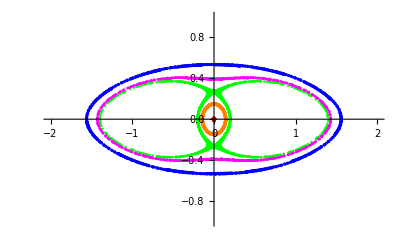
-Graphics-(α,k)=(0.52,0.03), exiting instability tongue

```mathematica
Labeled[Show[orb20,orb21,orb22,orb24,orb25],Style["(α,k)=(0.52,0.03), exiting instability tongue","Graphics"]]
```